```mathematica
Clear["Global`*"]
```

## Input

```mathematica
(* units *)
fm=5.0676896;

(* structures *)
J=0;
L=0;
s1=1/2;
s2=1/2;
Cij=-4/3;

(* masses *)
mc=1.659;
mb=5.036;
mi=mc;
mj=mc;

(* GIC parameters *)
αscc=0.47;
αscb=0.362;
αsbb=0.333;
αs=αscc;
b=0.165;
c=-0.409;
σ=1.22;

(* GEM parameters *)
nmax=20;
rmin=0.10fm;
rmax=10.0fm;
```

## Spin

```mathematica
NineJSymbol[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,J_}]:=
Module[{res,x,xmin,xmax},
If[j1<0||j2<0||j12<0||j3<0||j4<0||j34<0||j13<0||j24<0||J<0,Return[0]];
If[j1+j2<j12||Abs[j1-j2]>j12||Mod[j1+j2+j12,1]≠0,Return[0]];
If[j3+j4<j34||Abs[j3-j4]>j34||Mod[j3+j4+j34,1]≠0,Return[0]];
If[j1+j3<j13||Abs[j1-j3]>j13||Mod[j1+j3+j13,1]≠0,Return[0]];
If[j2+j4<j24||Abs[j2-j4]>j24||Mod[j2+j4+j24,1]≠0,Return[0]];
If[j12+j34<J||Abs[j12-j34]>J||Mod[j12+j34+J,1]≠0,Return[0]];
If[j13+j24<J||Abs[j13-j24]>J||Mod[j13+j24+J,1]≠0,Return[0]];
xmin=Max[Abs[j2-j34],Abs[j3-j24]];
xmax=Min[j2+j34,j3+j24];
res=Sum[(-1)^(2*x)*(2*x+1)*
SixJSymbol[{j1,j2,j12},{j34,J,x}]*SixJSymbol[{j3,j4,j34},{j2,x,j24}]*SixJSymbol[{j13,j24,J},{x,j1,j3}]
,{x,xmin,xmax}];
Return[res]]
SdS[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(S(S+1)-s1(s1+1)-s2(s2+1))/2*KroneckerDelta[{s1p,s2p,Sp,Lp},{s1,s2,S,L}]
S1L[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(-1)^(S+Lp+J)SixJSymbol[{Sp,S,1},{L,Lp,J}]*(-1)^(s1p+s2p+S+1)√((2Sp+1)(2S+1))SixJSymbol[{s1,s1p,1},{Sp,S,s2p}]*√((2s1+1)(s1+1)s1)*√((2L+1)(L+1)L)*KroneckerDelta[{s1p,s2p,Lp},{s1,s2,L}]
S2L[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(-1)^(S+Lp+J)SixJSymbol[{Sp,S,1},{L,Lp,J}]*(-1)^(s1+s2+Sp+1)√((2Sp+1)(2S+1))SixJSymbol[{s2,s2p,1},{Sp,S,s1p}] √((2s2+1)(s2+1)s2)*√((2L+1)(L+1)L)*KroneckerDelta[{s1p,s2p,Lp},{s1,s2,L}]
Ten[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=
(-1)^(S+Lp+J)√((24π)/5)SixJSymbol[{Sp,S,2},{L,Lp,J}]*
√(5(2Sp+1)(2S+1))NineJSymbol[{s1p,s1,1},{s2p,s2,1},{Sp,S,2}] √((2s1+1)(s1+1)s1)√((2s2+1)(s2+1)s2)*
(-1)^Lp √((5(2Lp+1)(2L+1))/(4π))ThreeJSymbol[{Lp,0},{2,0},{L,0}]*KroneckerDelta[{s1p,s2p},{s1,s2}]
```

```mathematica
(*j-j*)
JJ={};
Do[If[Abs[jl-s2]≤J≤jl+s2,JJ=Join[JJ,{{s1,s2,jl,L}}]],{jl,Abs[L-s1],L+s1}]
JJ;
trans=Table[S=SL[[i,3]];jl=JJ[[j,3]];(-1)^(s2+L+S+jl)√((2S+1)(2jl+1))SixJSymbol[{s2,s1,S},{L,J,jl}],{j,1,Length[JJ]},{i,1,Length[SL]}];

(*S-L*)
SL={};
Do[If[Abs[S-L]≤J≤S+L,SL=Join[SL,{{s1,s2,S,L}}]],{S,Abs[s1-s2],s1+s2}]
SL
trans=Table[KroneckerDelta[f,i],{f,1,Length[SL]},{i,1,Length[SL]}]
```

{{1/2,1/2,0,0}}

{{1}}

```mathematica
OSdS=Table[SdS[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OS1L=Table[S1L[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OS2L=Table[S2L[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OTen=Table[Ten[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OCen=Table[KroneckerDelta[SL[[f]],SL[[i]]],{f,1,Length[SL]},{i,1,Length[SL]}];

OSdS=Transpose[trans].OSdS.trans//Simplify
OS1L=Transpose[trans].OS1L.trans//Simplify
OS2L=Transpose[trans].OS2L.trans//Simplify
OTen=Transpose[trans].OTen.trans//Simplify
OCen=Transpose[trans].OCen.trans//Simplify
```

SixJSymbol::tri: SixJSymbol[{0,0,1},{0,0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

SixJSymbol::tri: SixJSymbol[{0,0,1},{0,0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

SixJSymbol::tri: SixJSymbol[{0,0,2},{0,0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

{{-3/4}}

{{0}}

{{0}}

{{0}}

{{1}}

## GEM

```mathematica
(* Gaussian basis *)
ν[n_]:=1/rmin^2(rmax/rmin)^((2-2n)/(nmax-1))
Rnlp[p_,n_,l_]:=(-ⅈ)^l 2^(-l/2-1/4)ν[n]^(-l/2-3/4)√(1/Gamma[l+3/2])p^l Exp[-p^2/(4 ν[n])]
Rnlr[r_,n_,l_]:=2^(l/2+5/4) ν[n]^(l/2+3/4)√(1/Gamma[l+3/2])r^l Exp[-r^2 ν[n]]
```

{{-0.409-0.233264 ⅇ^(-1.4884 r^2)-0.626667/r+0.165 r}}

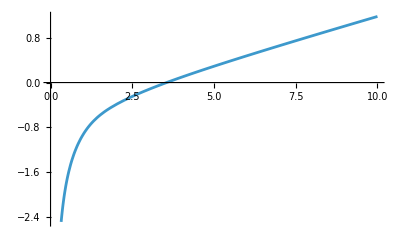

```mathematica
(* Hamiltonium *)
T=(p^2/(2mi)+p^2/(2mj)+mi+mj)*OCen;
Vconf=(Cij αs/r-3/4 Cij*b*r-3/4 Cij*c)*OCen;
Vhyp=(2αs)/(3mi*mj)((8*σ^3)/(3 π^(1/2))Exp[-σ^2 r^2]*OSdS+1/r^3*OTen);
Vsoν=(2 αs)/(3 r^3)(OS1L/mi^2-OS2L/mj^2-(OS1L-OS2L)/(mi*mj));
Vsos=1/(2r)D[Vconf,{r,1}](-OS1L/mi^2+OS2L/mj^2);
V=Vconf+Vhyp+Vsoν+Vsos
Plot[V,{r,0,10}]
```

```mathematica
NSL={};
Do[NSL=Join[NSL,{{n,SL[[i,4]],i}}],{i,1,Length[SL]},{n,1,nmax}];
NSL
Tfi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*T[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
Vfi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*V[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
Nfi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
Hfi=Tfi+Vfi;
```

{{1,0,1},{2,0,1},{3,0,1},{4,0,1},{5,0,1},{6,0,1},{7,0,1},{8,0,1},{9,0,1},{10,0,1},{11,0,1},{12,0,1},{13,0,1},{14,0,1},{15,0,1},{16,0,1},{17,0,1},{18,0,1},{19,0,1},{20,0,1}}

{3.05757,3.67721,4.10029,4.45463,4.77074,5.06604,5.40135,5.6473,6.15648,6.65083,7.02953,8.11067,8.77515,9.57807,11.4954,12.4829,14.1183,17.9515,19.3007,32.0593}

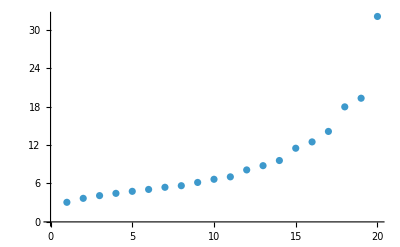

```mathematica
{e,v}=Transpose[Sort[Transpose[Eigensystem[{Hfi,Nfi}]],#1[[1]]<#2[[1]]&]];
v=v/Sqrt[Diagonal[v.Nfi.Transpose[v]]];(*归一化*)
e
ListPlot[e]
```

0.460625 ⅇ^(-3.89386 r^2)-0.744453 ⅇ^(-2.39802 r^2)+1.08197 ⅇ^(-1.47682 r^2)-0.785501 ⅇ^(-0.909497 r^2)+0.885202 ⅇ^(-0.560112 r^2)-0.33021 ⅇ^(-0.344944 r^2)+0.57846 ⅇ^(-0.212433 r^2)-0.0328075 ⅇ^(-0.130827 r^2)+0.162266 ⅇ^(-0.0805693 r^2)-0.0733833 ⅇ^(-0.0496184 r^2)+0.0384161 ⅇ^(-0.0305574 r^2)-0.0194065 ⅇ^(-0.0188187 r^2)+0.00944815 ⅇ^(-0.0115895 r^2)-0.00442318 ⅇ^(-0.00713736 r^2)+0.00197454 ⅇ^(-0.00439553 r^2)-0.000824577 ⅇ^(-0.00270698 r^2)+0.000310498 ⅇ^(-0.00166709 r^2)-0.0000985294 ⅇ^(-0.00102667 r^2)+0.0000231282 ⅇ^(-0.000632275 r^2)-2.94226×10^-6 ⅇ^(-0.000389386 r^2)

1.22758

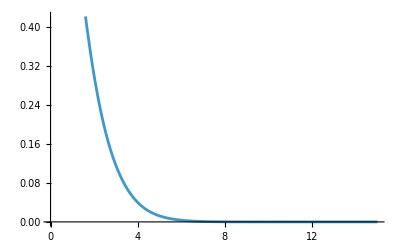

0.370337

```mathematica
n=1;
ϕr=Sum[v[[n,i]]*Rnlr[r,i,L],{i,1,Length[v]}]//Simplify
ϕr/.r->0 
Plot[ϕr,{r,0,15}]
rms=Sqrt[NIntegrate[ϕr^2*r^4,{r,0,Infinity}]];
rms/fm
```

```mathematica
(* SHO *)
Rnlp[p_,n_,l_,β_]:=((-1)^n*(-ⅈ)^l)/β^(3/2)*√((2*n!)/Gamma[n+l+3/2])*(p/β)^l ⅇ^(-p^2/(2*β^2))*LaguerreL[n,l+1/2,p^2/β^2]
Rnlr[r_,n_,l_,β_]:=β^(3/2)*√((2*n!)/Gamma[n+l+3/2])*(r*β)^l Exp[-(r^2*β^2)/2]*LaguerreL[n,l+1/2,r^2*β^2]
Solve[NIntegrate[ϕr^2*r^4,{r,0,Infinity}]==Integrate[Rnlr[r,n-1,L,β]^2*r^4,{r,0,Infinity}]&&β>0,β]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→0.652586}}